# more carefully estimate trap depth and frequencies...

#### Data

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
λtrap=976 nm;
m=132.90545 amu;23amu;
Needs["ErrorBarLogPlots`"];
SetDirectory[NotebookDirectory[]];

params=Import["params.csv"][[1]];
survCs=Transpose[Import["surv.csv"]][[;;,4]]; (*3 if Na, 4 if Cs*)
survNa=Transpose[Import["surv.csv"]][[;;,3]]; (*3 if Na, 4 if Cs*)

surv=survCs;

survErr=Transpose[Import["survErr.csv"]][[;;,4]];
data0=Thread[{Thread[{params,surv}],ErrorBar[#]&/@survErr}];
```

```mathematica
{Ttrap,frad1,frad2,fax}={2.3138810080893077mK,150kHz,140kHz,27.5kHz};{.311mK,131.837 kHz,123.048 kHz,24.1701 kHz};

TList=Range[50,150,10]uK;Range[5,200,5]uK; (*atom temp guesses. assuming: T in uK, and they are in increasing order*)

Utrap = kB Ttrap;

w01=√(Utrap/(frad1^2 m π^2)); (*0.67, 133 amu, 71kHz gives 917 nm*)
w02=√(Utrap/(frad2^2 m π^2));
w1[z_]:=w01√(1+((λtrap z)/(π w01^2))^2);
w2[z_]:=w02√(1+((λtrap z)/(π w02^2))^2);
U[r_]:=Utrap(1-(w01 w02)/(w1[r[[3]]]w2[r[[3]]])Exp[-2 r[[1]]^2/w1[r[[3]]]^2]Exp[-2 r[[2]]^2/w2[r[[3]]]^2]);
(*w0^2/w[r[[3]]]^2 Exp[-2 (r[[1]]^2+r[[2]]^2)/w[r[[3]]]^2]*)
Δt=Sort[params] ;
nSim=1000; (*number of realizations*)
```

```mathematica
scale=surv[[1]]; (*maximum survival rate, haven't appended error bars yet*)
data=data0[[1;;]]; (*don't use all points to fit?*)
Δt=Δt[[1;;]];
sigma=1.Flatten[survErr[[1;;]]];
mcTOFfit=Reap[
Do[

coordsInit=Reap[
Do[(*loop nSim times*)
coordsInitSingle=Reap[
Do[(*loop over 3 axes*)
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
nCutoff=10 Ceiling[nbar];
Pn=Table[nbar^n/(nbar+1)^(n+1),{n,0,nCutoff}]; (*probability distribution*)
Cn=Accumulate[Pn]; (*cumulative distr*)

(*sample n from a probability distribution Pn*)
(*compare random number to cumulative distribution. put 1 if positive, 0 if negative.*)
listpn=Boole[Positive[#]]&/@(RandomReal[]-Cn);
(*the total of this list gives the corresponding n*)
n=Total[listpn];


ϵn=(n+1/2)ℏ 2π f;

(*randomly sample mixing angle b/t v and x*)
(*ie randomly distribute the energy b/t position and velocity. *)
θ=RandomReal[2π];
xtemp=(√ϵn Sin[θ])/(√(1/2 m)(2π f));
vtemp=(√ϵn Cos[θ])/(√(1/2 m)); 

coordstemp={xtemp,vtemp};

Sow[coordstemp],
{f,{frad1,frad2,fax}}
]
][[2,1]];

(*list of the form {{x,y,z},{vx,vy,vz}}*)
coordsInitSingle=Transpose[coordsInitSingle];
Sow[coordsInitSingle]
,{j,nSim}]
][[2,1]];

rInit=Transpose[coordsInit][[1]];
vInit=Transpose[coordsInit][[2]];
KInit=m/2 Norm[#]^2&/@vInit;

(*sort by realizations. ie each list scans thru all Δt for a single realization*)
rFin=Transpose[rInit+vInit #&/@Δt];
PFin=U[#]&/@#&/@rFin;

EFin=(#1+#2)&[PFin,KInit];
SurvProb=Thread[{Δt/us,scale Total[#]&/@Transpose[Boole[Positive[Utrap-EFin]]]/Length[rInit]}];

chiSquare=Total[((SurvProb-data[[;;,1]])^2)[[;;,2]]/sigma^2];
Sow[{T/uK,SurvProb,chiSquare}]
,{T,TList}]
][[2,1]];
```

nbar={12.0086, 12.9012, 67.6938}+/-{0.263339, 0.30038, 7.45284}

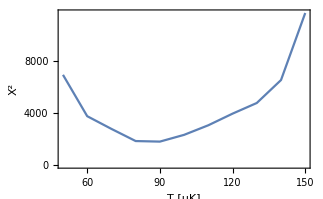

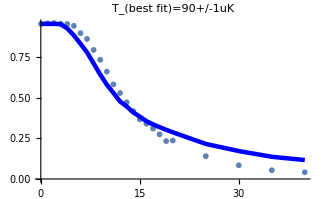

```mathematica
chiSquares=mcTOFfit[[;;,3]];
PosBestFit=Flatten[Position[chiSquares,Min[chiSquares]]];
TBestFit=mcTOFfit[[;;,1]][[PosBestFit]][[1]];
chisquaremin=chiSquares[[PosBestFit]][[1]];

(*list of triplets: {"param name", est val, error.,chisquaremin}*)

fitParams={"T [uK]",TBestFit,chisquareErr,chisquaremin};

(*only append if fit is good. check goodness of fit!!*)
chisquarefitfn=a (x-x0)^2+b;
(*only fit to the min and 2 points on either side*)
chiSquaresNearMin=mcTOFfit[[;;,{1,3}]][[PosBestFit[[1]]-2;;PosBestFit[[1]]+2]]; 
chisquarenlm=NonlinearModelFit[chiSquaresNearMin,chisquarefitfn,{a,{ x0,TBestFit}, {b,chisquaremin}},x];
chisquarefit=chisquarenlm["BestFitParameters"];
chisquareErr=√(( a/.chisquarefit)^-1); (*this is the +/- error in uK of the extracted temperature*)
(*error taken to be √(2(∂_T ∂_T Χ^2)^-1)from energy distr of single atom... paper*)
dftrap=3 kHz;
nbar=1/(Exp[(ℏ 2π f)/(kB T)]-1);
Δnbar=√((D[nbar, T])^2(chisquareErr uK)^2+(D[nbar, f])^2(dftrap)^2)/.T->TBestFit uK/.f->{frad1,frad2,fax};
Print["nbar="<>ToString[nbar/.T->TBestFit uK/.f->{frad1,frad2,fax}]<>"+/-"<>ToString[Δnbar]];

data2=data0;
For[i=1,i<=Length[data],i++,
data2[[i,1,1]]=data[[i,1,1]]/us];

Show[{ListPlot[mcTOFfit[[;;,{1,3}]],Joined->True,FrameLabel->{"T [uK]","Χ^2","T_(best fit)="<>ToString[TBestFit]<>"+/-"<>ToString[Round[chisquareErr]]<>"uK"},Frame->True](*,
Plot[chisquarefitfn/.chisquarefit,{x,Min[TList/uK],Max[TList/uK]},PlotStyle->Red]*)
}]

Show[
{ErrorListPlot[data2,PlotLabel->"T_(best fit)="<>ToString[TBestFit]<>"+/-"<>ToString[Round[chisquareErr]]<>"uK"],
ListPlot[mcTOFfit[[PosBestFit,2]][[1]],Joined->True,PlotStyle->{Thickness[.01],Blue},Frame->{True,True},Axes->False,FrameLabel->{"t[us]","survival rate"},PlotRange->All]
}
]
```